# Data analysis of Open Dynamics

```mathematica
SetDirectory[NotebookDirectory[]];
datawigner=Import["output/wignerfunction3_out.dat"];
wg=Import["output/wignerresults.dat"];
datasp=Import["output/survivalprobability.dat"];
datale=Import["output/loschmidt_echo.dat"];
```

#### Classical Trajectories

```mathematica
(*Classical Hamiltonian*)
Δ=-2;
ϵ=0.0;
Kp=1;
ω=17.1;
ξ=0.5;
H[q_,p_,t_]=-(Δ/2)*(q^2+p^2)+(Kp/4)*(q^2+p^2)^2-ϵ*(q^2-p^2);
HD[q_,p_,t_]=-(Δ/2)*(q^2+p^2)+(Kp/4)*(q^2+p^2)^2-ϵ*(q^2-p^2)+ξ*(q^2+p^2)*Cos[ω*t]/2;
```

```mathematica
(*Solving the Hamiltons equation*)
pin=2.0;
qin=-2;
tf=20000;
T=2 Pi/ω;
sol=NDSolve[{D[q[t],t]==D[H[q[t],p[t],t],p[t]],D[p[t],t]==-D[H[q[t],p[t],t],q[t]],q[0]==qin,p[0]==pin},{q,p},{t,0,tf}];
solt=NDSolve[{D[q[t],t]==D[HD[q[t],p[t],t],p[t]],D[p[t],t]==-D[HD[q[t],p[t],t],q[t]],q[0]==qin,p[0]==pin},{q,p},{t,0,tf}];
```

```mathematica
(*Classical trajectories and Poncaire sections*)
Tint=0.1;
T=2Pi/ω;
qp=Table[{q[t],p[t]}/.sol[[1]]/.t->i,{i,0,tf,Tint}];
qpt=Table[{q[t],p[t]}/.solt[[1]]/.t->i,{i,0,tf,T}];
```

```mathematica
ct=ListPlot[qp,PlotStyle->Darker[Green]]
```

-Graphics-

#### TWA

#### Wigner function

```mathematica
(*Color for the Wigner function*)
FCo[t_]=Piecewise[{{ RGBColor[1,(2t)^3,(2t)^3],0<=t<=1/2},{ RGBColor[(1-2(t-1/2)),(1-2(t-1/2)),1],1/2<t<=1}}];
```

```mathematica
wigner2=Show[ListDensityPlot[datawigner,PlotRange->{{-6,6},{-6,6},All},Frame->True,LabelStyle->{Black,24},ColorFunction->(FCo[1-0.5/0.35(#+0.35)]&),ColorFunctionScaling->False(*,PlotLegends->Automatic*)],ListPlot[{},PlotStyle->Darker[Green]],ct]
```

-Graphics-

```mathematica
Export["wigner_Closed_t6.png",wigner2]
```

wigner_Closed_t6.png

```mathematica
wn=Table[{wg[[i,1]],wg[[i,3]]-1*wg[[1,3]]},{i,1,Length[wg]}];
```

```mathematica
wg
```

{{0.,0.977619,-0.022308},{3.64159,0.964772,0.1014},{6.78319,0.963043,-0.010075},{9.92478,0.953018,-0.043348},{13.0664,0.953643,-0.046356},{16.208,0.954233,-0.045766},{19.3496,0.946358,-0.053641}}

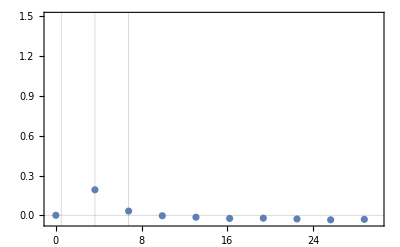

```mathematica
(*Negativities*)
Show[ListPlot[{wn},PlotRange->{{-0.5,30},{-0.05,1.5}},Joined->False,Frame->True,GridLines->{{0.5,0.5+π,0.5+2*π},{0}},LabelStyle->Directive[Bold, Medium]]]
```

```mathematica
Tl1={{0.04,4*π},{0.05,3*π}};
```

#### Survival amplitude

```mathematica
datsp=datasp;
```

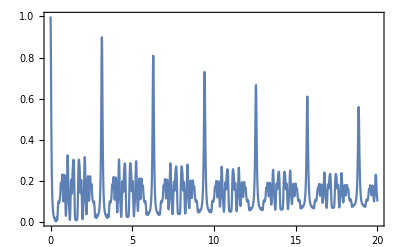

```mathematica
(*Survival probability*)
figsp=Show[ListPlot[{datsp},PlotRange->{{0,20},All},Joined->True,Frame->True,GridLines->{{π/2,3π/2,5π/2},{}},GridLinesStyle->{{Dashed,Red,Thickness[0.007]},{}},LabelStyle->{Black,18}]]
```

```mathematica
Export["SP_openKerr.png",figsp]
```

SP_openKerr.png

```mathematica
ampcomp=Table[datale[[i,2]]+I*datale[[i,3]],{i,1,Length[datale]}];
dataca=Table[{datale[[i,1]],-Log[Abs[ampcomp[[i]]]^2]},{i,1,Length[datale]}];
```

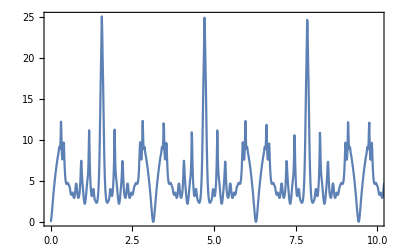

```mathematica
figsa=ListPlot[{dataca},PlotRange->{{0,10},All},PlotLegends->{},Frame->True,Joined->True,LabelStyle->{18,Black},FrameLabel->{},GridLines->{{π/2,3π/2,5π/2},{}},GridLinesStyle->{{Dashed,Red,Thickness[0.007]},{Thick,Red,Dashed}}]
```

```mathematica
Export["LE_openKerr.png",figsa]
```

LE_openKerr.png

```mathematica
ampcomp=Table[datasact[[i,3]]+I*datasact[[i,4]],{i,1,Length[datasact]}];
datact=Table[{datasact[[i,2]],datasact[[i,1]],Log[Abs[ampcomp[[i]]]^2]},{i,1,Length[datasact]}];
```

```mathematica
fig2=ListDensityPlot[datact,GridLines->{{0},{}},LabelStyle->{18,Black},GridLinesStyle->{{Dashed,Black,Thick},{Thick,Red,Dashed}},PlotRange->{{-0.1,0.1},{0,10},{-15,15}},PlotLegends->Automatic,ColorFunction->"TemperatureMap",LabelStyle->"Subtitle"]
```

-Graphics-